```mathematica
data=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi.csv"];
```

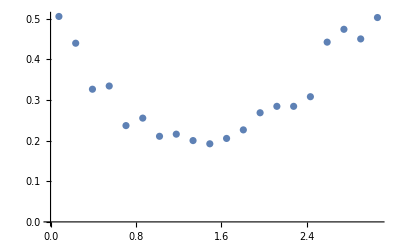

```mathematica
ListPlot[data]
```

```mathematica
Total[data[[All,2]]*ArrayPad[Differences[data[[All,1]]],{0,1},"Reversed"]]
```

1.

## [1.0, 1.4], [1.4, 2.0], N = 1 000 000

```mathematica
data1=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1.csv"];
```

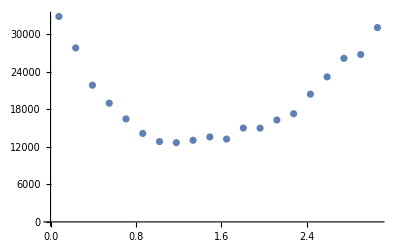

```mathematica
plot1=ListPlot[data1]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr1.pdf",plot1]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr1.pdf

## [2.4, 2.8], [2.8, 5.0], N = 1 000 000

```mathematica
data2=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_2.csv"];
```

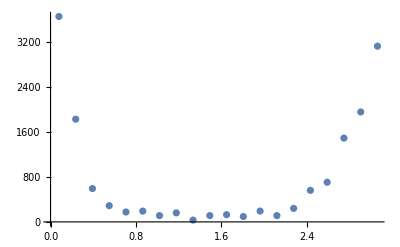

```mathematica
plot2=ListPlot[data2]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf",plot2]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf